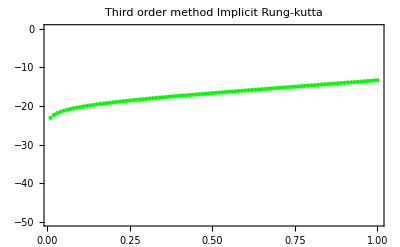

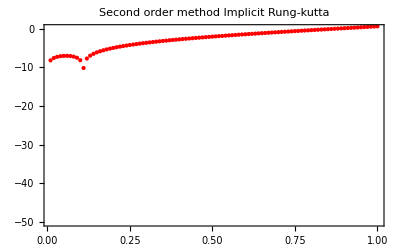

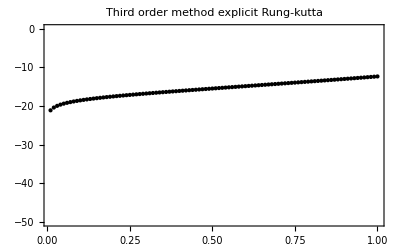

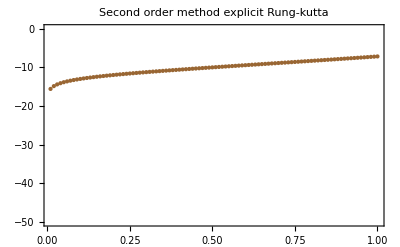

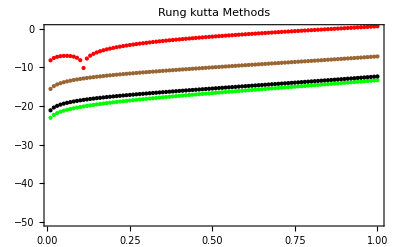

```mathematica
(*Third order method  Implicit Rung-kutta *)   
(*{{{y'=e^t y(t)+-e^(2t)}, {y(0)=1}} tϵ⌊0,1⌋
*)
(*  Subscript[k, 1] =h f(Subscript[t, n],Subscript[y, n]  )
 Subscript[k, 2] =h f(Subscript[t, n]+2/3 h+Subscript[y, n] +1/3 Subscript[k, 1] +1/3 Subscript[k, 2] )
Subscript[y, n+1] =Subscript[y, n] +1/4 Subscript[k, 1]+ 3/4 Subscript[k, 2] *)                                   
f[t_,y_]:=Exp[t]*y-Exp[2* t];
eq=yy'[t]==Exp[t]*yy[t]-Exp[2 t];
sol=DSolve[{eq,yy[0]==1},yy[t],t];
exact=sol[[1]][[1]][[2]];
h=Input[" Enter lentgh of interval="];
y[0]=1;
n=1/h;
Do[
k1= h*f[i*h,y[i]];
knew2=N[NSolve [kk2==  h*f[i*h+(2/3)*h,y[i]+(1/3)*k1+(1/3)*kk2] ]] ;   
y[i+1]= y[i]+(1/4)*k1+(3/4)*knew2[[1]][[1]][[2]];   
,{i,0,n-1}];
Table[y[i],{i,0,n}];
ar=Table[(exact/.t->(i*h))-y[i],{i,0,n}];
ar1=Table[{h *i,Log[Abs[ar[[i+1]]]]},{i,1,n}];
im3=ListPlot[ar1,PlotRange->{-50,0},PlotStyle->Green,Frame->True,PlotLabel->"Third order method  Implicit Rung-kutta"(*,PlotMarkers->"°"*)]
(* -------------------------------------------------------*)
(*Second order method  Implicit Rung-kutta *)
(*Subscript[k, 1] =h f(Subscript[t, n]+1/2 h+Subscript[y, n] +1/2 Subscript[k, 1]  );
  Subscript[k, 2] =h f(Subscript[t, n],Subscript[y, n]  ) ;
 Subscript[y, n+1] =Subscript[y, n] +Subscript[k, 1] ; *)                                                         f[t_,y_]:=Exp[t]*y-Exp[2* t];
eq=yy'[t]==Exp[t]*yy[t]-Exp[2 t];
sol=DSolve[{eq,yy[0]==1},yy[t],t];
exact=sol[[1]][[1]][[2]];
h=Input[" Enter lentgh of interval="];
y[0]=1;
n=1/h;
Do[
knew1=N[NSolve [kk1==  h*f[i*h+(1/2)*h,y[i]+(1/2)*k1] ]] ;
k2= h*f[i*h,y[i]];   
y[i+1]= y[i]+(1/2)*knew1[[1]][[1]][[2]];   
,{i,0,n-1}];
Table[y[i],{i,0,n}];
ar=Table[(exact/.t->(i*h))-y[i],{i,0,n}];
ar1=Table[{h *i,Log[Abs[ar[[i+1]]]]},{i,1,n}];
im2=ListPlot[ar1,PlotRange->{-50,0},PlotStyle->Red,Frame->True,PlotLabel->"Second order method  Implicit Rung-kutta"(*,PlotMarkers->"Λ"*)]
(* -------------------------------------------------------*)
(*Third order method  explicit Rung-kutta *)
(* NEARLY OPTIMAL METHOD*)
 (*  Subscript[k, 1] =h f(Subscript[t, n],Subscript[y, n]  )
 Subscript[k, 2] =h f(Subscript[t, n]+1/2 h+Subscript[y, n] +1/2 Subscript[k, 1]  )
 Subscript[k, 3] =h f(Subscript[t, n]+3/4 h+Subscript[y, n] +3/4 Subscript[k, 2]  )
Subscript[y, n+1] =Subscript[y, n] +2/9 Subscript[k, 1]+ 3/9 Subscript[k, 2] + 4/9 Subscript[k, 3]
 *) 
f[t_,y_]:=Exp[t]*y-Exp[2* t];
eq=yy'[t]==Exp[t]*yy[t]-Exp[2 t];
sol=DSolve[{eq,yy[0]==1},yy[t],t];
exact=sol[[1]][[1]][[2]];
h=Input[" Enter lentgh of interval="];
y[0]=1;
n=1/h;
Do[
k1= h*f[i*h,y[i]] ;
 k2=  h*f[i*h+1/2*h,y[i]+1/2*k1] ;
k3=  h*f[i*h+3/4*h,y[i]+3/4*k2] ;    
y[i+1]= y[i]+2/9*k1+3/9*k2+4/9*k3
,{i,0,n-1}];
Table[y[i],{i,0,n}];
ar=Table[(exact/.t->(i*h))-y[i],{i,0,n}];
ar1=Table[{h *i,Log[Abs[ar[[i+1]]]]},{i,0,n}];
ex3=ListPlot[ar1,PlotRange->{-50,0},PlotStyle->Black,Frame->True,PlotLabel->"Third order method  explicit Rung-kutta"(*,
PlotMarkers->"*"*)]
(*-------------------------------------------------------*)
(*Second order method  explicit Rung-kutta *)
 (*  Subscript[k, 1] =h f(Subscript[t, n],Subscript[y, n]  )
 Subscript[k, 2] =h f(Subscript[t, n]+2/3 h+Subscript[y, n] +2/3 Subscript[k, 1]  )
Subscript[y, n+1] =Subscript[y, n] +1/4 Subscript[k, 1]+ 3/4 Subscript[k, 2]
 *) 
f[t_,y_]:=Exp[t]*y-Exp[2* t];
eq=yy'[t]==Exp[t]*yy[t]-Exp[2 t];
sol=DSolve[{eq,yy[0]==1},yy[t],t];
exact=sol[[1]][[1]][[2]];
h=Input[" Enter lentgh of interval="];
y[0]=1;
n=1/h;
Do[
k1= h*f[i*h,y[i]] ;
 k2=  h*f[i*h+2/3*h,y[i]+2/3*k1] ;    
y[i+1]= y[i]+1/4*k1+3/4*k2
,{i,0,n-1}];
Table[y[i],{i,0,n}];
ar=Table[(exact/.t->(i*h))-y[i],{i,0,n}];
ar1=Table[{h *i,Log[Abs[ar[[i+1]]]]},{i,0,n}];
ex2=ListPlot[ar1,PlotRange->{-50,0},PlotStyle->Brown,Frame->True,PlotLabel->"Second order method  explicit Rung-kutta"(*,PlotMarkers->"*"*)]
(* -------------------------------------------------------*)
(*Forth order method  explicit Rung-kutta *)
 (*  Subscript[k, 1] =h f(Subscript[t, n],Subscript[y, n]  )
 Subscript[k, 2] =h f(Subscript[t, n]+ h+Subscript[y, n] + Subscript[k, 1]  )
 Subscript[k, 3] =h f(Subscript[t, n]+ h+Subscript[y, n] + Subscript[k, 2]  )
 Subscript[k, 4] =h f(Subscript[t, n]+1/2 h+Subscript[y, n] +1/2 Subscript[k, 3]  )
Subscript[y, n+1] =Subscript[y, n] +1/6 Subscript[k, 1]+ 2/6 Subscript[k, 2] + 2/6 Subscript[k, 3]+1/6 Subscript[k, 4]
 *) 
f[t_,y_]:=Exp[t]*y-Exp[2* t];
eq=yy'[t]==Exp[t]*yy[t]-Exp[2 t];
sol=DSolve[{eq,yy[0]==1},yy[t],t];
exact=sol[[1]][[1]][[2]];
h=Input[" Enter lentgh of interval="];
y[0]=1;
n=1/h;
Do[
k1= h*f[i*h,y[i]] ;
 k2=  h*f[i*h+h,y[i]+k1] ;
k3=  h*f[i*h+h,y[i]+k2] ;    
k4=  h*f[i*h+1/2*h,y[i]+1/2*k2] ;   
y[i+1]= y[i]+1/6*k1+2/6*k2+2/6*k3+1/6*k4
,{i,0,n-1}];
Table[y[i],{i,0,n}];
ar=Table[(exact/.t->(i*h))-y[i],{i,0,n}];
ar1=Table[{h *i,Log[Abs[ar[[i+1]]]]},{i,0,n}];
ex4=ListPlot[ar1,PlotRange->{-50,0},PlotStyle->Yellow,Frame->True,PlotLabel->"Forth order method  explicit Rung-kutta"(*,
PlotMarkers->"*"*)]
Show[{im3,im2,ex3,ex2,ex4},PlotLabel->"Rung kutta Methods"]
```